```mathematica
ClearAll["Global`*"]
(*別のnbファイルの内容を取り込み，後で利用する*)
NotebookEvaluate[FileNameJoin[{NotebookDirectory[],"mathematica_plot_options.nb"}]];
```

Available:plot2Doption
plot3Doption
framelabel[xlabel_String,ylabel_String,size_:20]
axeslabel2D[xlabel_String,ylabel_String,size_:20]
axeslabel3D[xlabel_String,ylabel_String,zlabel_String,size_:20]
axeslabel[labels_List,size_: 20]
importData
jsonInfo
interpolateAndFourier
interpolateAndFourierTr
MyFourier[list_,n_]
MyInverseFourier[list_,n_]
MyDiscreteConvolve[f_,g_]
MyDiscreteConvolveUsingCn[FourierGF_]
getOmegaFromKandDepth
getTFromLandDepth

## PITCH

```mathematica
names={"dataMP1d5pitch1","dataMP1d5pitch2","dataMP3d0pitch1","dataMP3d0pitch2","dataMP5d0pitch1","dataMP5d0pitch2"}
```

{dataMP1d5pitch1,dataMP1d5pitch2,dataMP3d0pitch1,dataMP3d0pitch2,dataMP5d0pitch1,dataMP5d0pitch2}

```mathematica
files=Table[names[[i]]<>".csv",{i,1,Length@names}]
DATA=Table[Import[FileNameJoin[{NotebookDirectory[],files[[i]]}],"CSV"],{i,1,Length[files],1}];
DATA=DATA[[;;,20;;60]];
```

{dataMP1d5pitch1.csv,dataMP1d5pitch2.csv,dataMP3d0pitch1.csv,dataMP3d0pitch2.csv,dataMP5d0pitch1.csv,dataMP5d0pitch2.csv}

```mathematica
(*関数定義*)
calculate[data_]:=Module[{min,max,m,xaxis,yaxis,ans,zaxis,M,anlgetable,timetable,a00,a01,a02,a10,a11,a12,a20,a21,a22,displacement},
min=1;
max=Length[data];

ydir[i_]:=Normalize[data[[i]][[8;;10]]-data[[i]][[2;;4]]];
zdir[i_]:=Normalize[Cross[data[[i]][[5;;7]]-data[[i]][[2;;4]],data[[i]][[8;;10]]-data[[i]][[2;;4]]]];
xdir[i_]:=Normalize[Cross[ydir[i],zdir[i]]];
xaxis=xdir[1];
yaxis=ydir[1];
zaxis=zdir[1];
(*カメラの座標系から水槽x,y,z座標へ変換するための，回転行列を計算する*)
m={{a00,a01,a02},{a10,a11,a12},{a20,a21,a22}};
ans=FindMinimum[Norm[m.xaxis-{1,0,0}]+Norm[m.yaxis-{0,1,0}]+Norm[m.zaxis-{0,0,1}],{a00,a01,a02,a10,a11,a12,a20,a21,a22}];
M=m/.ans[[2]];
(*table=Table[{data[[i,1]],VectorAngle[M.zdir[i],{0,0,1}]},{i,1,100}];*)

anlgetable=Table[VectorAngle[M.zdir[i],{0,0,1}],{i,min,max}];
timetable=Table[data[[i,1]],{i,min,max}];
{anlgetable,timetable,M,{xaxis,yaxis,zaxis},{min,max}}
]

inv[x_]:=If[Abs[x]>10^-10,1/x,1/10^-10];
```

Part::partw: {{{1.54853,223.19,292.752,16.5101,25.3858,43.9695,14.0611,350.057,114.947,305.684},{1.59607,224.698,294.324,16.6216,215.944,-74.4156,32.9221,346.41,113.75,302.188},«7»,{1.99623,226.227,297.959,20.4082,220.234,-70.7285,32.9801,350.057,114.316,304.105},«31»},«4»,{{1.54365,«8»,212.162},«10»}}の部分8は存在しません．

Part::take: {{{1.54853,223.19,292.752,16.5101,25.3858,43.9695,14.0611,350.057,114.947,305.684},{1.59607,224.698,294.324,16.6216,215.944,-74.4156,32.9221,346.41,113.75,302.188},«7»,{1.99623,226.227,297.959,20.4082,220.234,-70.7285,32.9801,350.057,114.316,304.105},«31»},«4»,{{1.54365,«8»,212.162},«10»}}の8から10の位置が取れません．

General::stop: この計算中に，Part::takeのこれ以上の出力は表示されません．

Normalize::nlnmt2: 第1引数が数でもベクトルでもないか，第2引数がどのような数値的引数に対しても常に非負の実数を返すノルム関数でないかのいずれかです．

Cross::nonn1: 引数はすべて同じ長さのベクトルでなければなりません．また引数の個数はそれぞれの引数の要素数よりも1少なくなければなりません．

Normalize::nlnmt2: 第1引数が数でもベクトルでもないか，第2引数がどのような数値的引数に対しても常に非負の実数を返すノルム関数でないかのいずれかです．

Cross::nonn1: 引数はすべて同じ長さのベクトルでなければなりません．また引数の個数はそれぞれの引数の要素数よりも1少なくなければなりません．

General::stop: この計算中に，Cross::nonn1のこれ以上の出力は表示されません．

Normalize::nlnmt2: 第1引数が数でもベクトルでもないか，第2引数がどのような数値的引数に対しても常に非負の実数を返すノルム関数でないかのいずれかです．

General::stop: この計算中に，Normalize::nlnmt2のこれ以上の出力は表示されません．

FindMinimum::nrnum: 関数の値+<<1053942376 bytes>>は{a00$78532,a01$78532,a02$78532,a10$78532,a11$78532,a12$78532,a20$78532,a21$78532,a22$78532} = {1.,1.,1.,1.,1.,1.,1.,1.,1.}において実数ではありません．

General::stop: この計算中に，FindMinimum::nrnumのこれ以上の出力は表示されません．

ReplaceAll::reps: {a00$78532,a01$78532,a02$78532,a10$78532,a11$78532,a12$78532,a20$78532,a21$78532,a22$78532}は置換規則のリストでも有効なディスパッチ表でもないため，置換には使用できません．

Part::partd: 部分指定{{{1.54853,223.19,292.752,16.5101,25.3858,43.9695,14.0611,350.057,114.947,305.684},{1.59607,224.698,294.324,16.6216,215.944,-74.4156,32.9221,346.41,113.75,302.188},«7»,{1.99623,226.227,297.959,20.4082,220.234,-70.7285,32.9801,350.057,114.316,304.105},«31»},{{«19»,«8»,«19»},«9»,«31»},«3»,{{«1»},«9»,«31»}}⟦8⟧⟦2,1⟧の長さはオブジェクトの深さを超えています．

Set::shape: {displacement,anlgetable,timetable,M,{xaxis,yaxis,zaxis},{min,max}}と{<<702652664 bytes>>}のリストは型が違います．

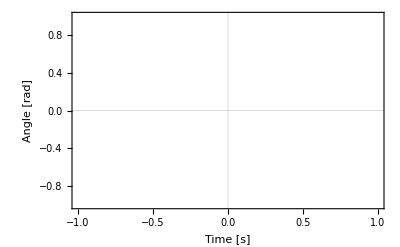

Symbol::argx: Symbolは0個の引数で呼ばれました．1つの引数が想定されています．

General::stop: この計算中に，Symbol::argxのこれ以上の出力は表示されません．

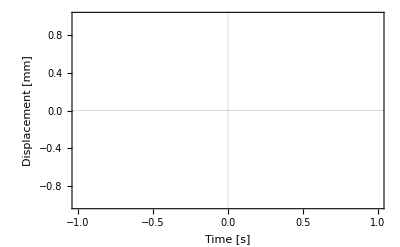

```mathematica
{displacement,anlgetable,timetable,M,{xaxis,yaxis,zaxis},{min,max}}=calculate[DATA[[8]]];
ListPlot[Transpose[{timetable,anlgetable}],Evaluate[plot2Doption],FrameLabel->{"Time [s]","Angle [rad]"}]
ListPlot[Table[Transpose[{timetable,displacement[[;;,i]]}],{i,{1,2,3}}],PlotLegends->Automatic,Evaluate[plot2Doption],FrameLabel->{"Time [s]","Displacement [mm]"}]
```

FindMinimum::lstol: 直線探索において刻み幅をAccuracyGoalとPrecisionGoalで指定された許容範囲内に減らしましたが，関数に十分な減少が見られませんでした．これらの許容範囲で満足するためには，MachinePrecision桁より高い作業精度が必要となることがあります．

Set::shape: {displacement,anlgetable,timetable,M,{xaxis,yaxis,zaxis},{min,max}}と{{7.53955×10^-9,0.570729,0.564896,0.00376925,0.566203,0.568833,0.587758,0.0101466,0.012009,0.578893,«31»},{1.54853,1.59607,1.64428,1.69316,1.74087,1.78861,1.83641,1.90085,1.94833,1.99623,«31»},{{«1»},{«1»},{«1»}},{{-0.687204,-0.713399,-0.137158},{0.350076,-0.490635,0.79795},{-0.636551,0.500339,0.58691}},{1,41}}のリストは型が違います．

FindMinimum::lstol: 直線探索において刻み幅をAccuracyGoalとPrecisionGoalで指定された許容範囲内に減らしましたが，関数に十分な減少が見られませんでした．これらの許容範囲で満足するためには，MachinePrecision桁より高い作業精度が必要となることがあります．

Set::shape: {displacement,anlgetable,timetable,M,{xaxis,yaxis,zaxis},{min,max}}と{{1.17367×10^-8,0.0158598,0.0269738,0.0121155,0.012103,0.952484,0.0139432,0.95152,0.952162,0.0178678,«31»},{1.54858,1.59663,1.64472,1.69319,1.74043,1.78855,1.83678,1.90107,1.94864,1.9966,«31»},{«1»},{{0.162395,-0.755942,-0.634177},{0.289411,-0.577951,0.76303},{-0.943329,-0.30745,0.124922}},{1,41}}のリストは型が違います．

FindMinimum::lstol: 直線探索において刻み幅をAccuracyGoalとPrecisionGoalで指定された許容範囲内に減らしましたが，関数に十分な減少が見られませんでした．これらの許容範囲で満足するためには，MachinePrecision桁より高い作業精度が必要となることがあります．

General::stop: この計算中に，FindMinimum::lstolのこれ以上の出力は表示されません．

Set::shape: {displacement,anlgetable,timetable,M,{xaxis,yaxis,zaxis},{min,max}}と{{Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,«31»},{1.54532,1.5934,1.64144,1.68984,1.73777,1.78509,1.83383,1.89747,1.94554,1.99357,«31»},{{1.24649,0.146124,0.759847},{0.978745,1.07363,1.02071},{1.24649,0.146124,0.759847}},{{0.,0.,0.},{-0.267747,0.927504,0.26086},{0.,0.,0.}},{1,41}}のリストは型が違います．

General::stop: この計算中に，Set::shapeのこれ以上の出力は表示されません．

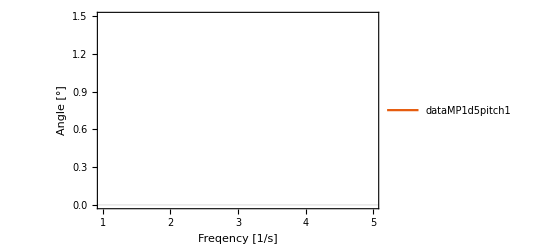

FindMinimum::lstol: 直線探索において刻み幅をAccuracyGoalとPrecisionGoalで指定された許容範囲内に減らしましたが，関数に十分な減少が見られませんでした．これらの許容範囲で満足するためには，MachinePrecision桁より高い作業精度が必要となることがあります．

Set::shape: {displacement,anlgetable,timetable,M,{xaxis,yaxis,zaxis},{min,max}}と{{7.53955×10^-9,0.570729,0.564896,0.00376925,0.566203,0.568833,0.587758,0.0101466,0.012009,0.578893,«31»},{1.54853,1.59607,1.64428,1.69316,1.74087,1.78861,1.83641,1.90085,1.94833,1.99623,«31»},{{«1»},{«1»},{«1»}},{{-0.687204,-0.713399,-0.137158},{0.350076,-0.490635,0.79795},{-0.636551,0.500339,0.58691}},{1,41}}のリストは型が違います．

FindMinimum::lstol: 直線探索において刻み幅をAccuracyGoalとPrecisionGoalで指定された許容範囲内に減らしましたが，関数に十分な減少が見られませんでした．これらの許容範囲で満足するためには，MachinePrecision桁より高い作業精度が必要となることがあります．

Set::shape: {displacement,anlgetable,timetable,M,{xaxis,yaxis,zaxis},{min,max}}と{{1.17367×10^-8,0.0158598,0.0269738,0.0121155,0.012103,0.952484,0.0139432,0.95152,0.952162,0.0178678,«31»},{1.54858,1.59663,1.64472,1.69319,1.74043,1.78855,1.83678,1.90107,1.94864,1.9966,«31»},{«1»},{{0.162395,-0.755942,-0.634177},{0.289411,-0.577951,0.76303},{-0.943329,-0.30745,0.124922}},{1,41}}のリストは型が違います．

FindMinimum::lstol: 直線探索において刻み幅をAccuracyGoalとPrecisionGoalで指定された許容範囲内に減らしましたが，関数に十分な減少が見られませんでした．これらの許容範囲で満足するためには，MachinePrecision桁より高い作業精度が必要となることがあります．

General::stop: この計算中に，FindMinimum::lstolのこれ以上の出力は表示されません．

Set::shape: {displacement,anlgetable,timetable,M,{xaxis,yaxis,zaxis},{min,max}}と{{Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,«31»},{1.54532,1.5934,1.64144,1.68984,1.73777,1.78509,1.83383,1.89747,1.94554,1.99357,«31»},{{1.24649,0.146124,0.759847},{0.978745,1.07363,1.02071},{1.24649,0.146124,0.759847}},{{0.,0.,0.},{-0.267747,0.927504,0.26086},{0.,0.,0.}},{1,41}}のリストは型が違います．

General::stop: この計算中に，Set::shapeのこれ以上の出力は表示されません．

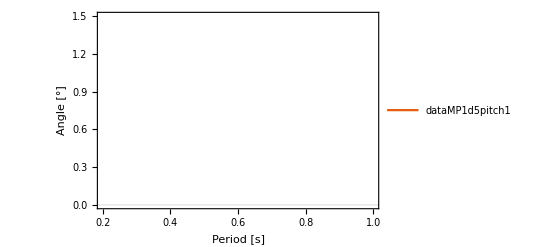

```mathematica
ListPlot[
Table[
Module[{},
{displacement,anlgetable,timetable,M,{xaxis,yaxis,zaxis},{min,max}}=calculate[DATA[[i]]];
Return[{#1,#2/π*180}&@@@interpolateAndFourier[timetable,anlgetable]]]
,{i,1,Length@DATA,1}]
,PlotLegends->names
,PlotRange->{{1,5},{0,1.5}}
,Evaluate[plot2Doption]
,FrameLabel->{"Freqency [1/s]","Angle [°]"}
]

(*フーリエ解析*)
ListPlot[
Table[
Module[{},
{displacement,anlgetable,timetable,M,{xaxis,yaxis,zaxis},{min,max}}=calculate[DATA[[i]]];
Return[{inv[#1],#2/π*180}&@@@interpolateAndFourier[timetable,anlgetable]]]
,{i,1,Length@DATA,1}]
,PlotLegends->names
,PlotRange->{{0.2,1},{0,1.5}}
,Evaluate[plot2Doption]
,FrameLabel->{"Period [s]","Angle [°]"}
]
```

## PISTON

```mathematica
names={"dataMP1d5piston1","dataMP1d5piston2","dataMP3d0piston1","dataMP3d0piston2","dataMP5d0piston1","dataMP5d0piston2"}
```

{dataMP1d5piston1,dataMP1d5piston2,dataMP3d0piston1,dataMP3d0piston2,dataMP5d0piston1,dataMP5d0piston2}

```mathematica
files=Table[names[[i]]<>".csv",{i,1,Length@names}]
DATA=Table[Import[FileNameJoin[{NotebookDirectory[],files[[i]]}],"CSV"],{i,1,Length[files],1}];
DATA=DATA[[;;,20;;60]];
```

{dataMP1d5piston1.csv,dataMP1d5piston2.csv,dataMP3d0piston1.csv,dataMP3d0piston2.csv,dataMP5d0piston1.csv,dataMP5d0piston2.csv}

```mathematica
(*関数定義*)
calculate[data_]:=Module[{min,max,m,xaxis,yaxis,ans,zaxis,M,anlgetable,timetable,a00,a01,a02,a10,a11,a12,a20,a21,a22,displacement},
min=1;
max=Length[data];

ydir[i_]:=Normalize[data[[i]][[8;;10]]-data[[i]][[2;;4]]];
zdir[i_]:=Normalize[Cross[data[[i]][[5;;7]]-data[[i]][[2;;4]],data[[i]][[8;;10]]-data[[i]][[2;;4]]]];
xdir[i_]:=Normalize[Cross[ydir[i],zdir[i]]];
xaxis=xdir[1];
yaxis=ydir[1];
zaxis=zdir[1];
(*カメラの座標系から水槽x,y,z座標へ変換するための，回転行列を計算する*)
m={{a00,a01,a02},{a10,a11,a12},{a20,a21,a22}};
ans=Quiet@FindMinimum[Norm[m.xaxis-{1,0,0}]+Norm[m.yaxis-{0,1,0}]+Norm[m.zaxis-{0,0,1}],{a00,a01,a02,a10,a11,a12,a20,a21,a22}];
M=m/.ans[[2]];
(*table=Table[{data[[i,1]],VectorAngle[M.zdir[i],{0,0,1}]},{i,1,100}];*)

displacement=Table[M.(data[[i]][[2;;4]]-data[[1]][[2;;4]]+data[[i]][[5;;7]]-data[[1]][[5;;7]]+data[[i]][[8;;10]]-data[[1]][[8;;10]]),{i,min,max}];

anlgetable=Table[VectorAngle[M.zdir[i],{0,0,1}],{i,min,max}];
timetable=Table[data[[i,1]],{i,min,max}];
{displacement,anlgetable,timetable,M,{xaxis,yaxis,zaxis},{min,max}}
]

inv[x_]:=If[Abs[x]>10^-10,1/x,1/10^-10];
```

```mathematica
{displacement,anlgetable,timetable,M,{xaxis,yaxis,zaxis},{min,max}}=calculate[DATA[[1]]];
{displacement,anlgetable,timetable,M,{xaxis,yaxis,zaxis},{min,max}}=calculate[DATA[[8]]];
ListPlot[Transpose[{timetable,anlgetable}],Evaluate[plot2Doption],FrameLabel->{"Time [s]","Angle [rad]"}]
ListPlot[Table[Transpose[{timetable,displacement[[;;,i]]}],{i,{1,2,3}}],PlotLegends->Automatic,Evaluate[plot2Doption],FrameLabel->{"Time [s]","Displacement [mm]"}]
```

Part::partw: {{{1.54545,191.123,269.31,85.6897,191.123,-104.828,93.4483,365.444,95.6044,329.011},{1.59285,190.031,266.4,83.4857,187.883,-101.356,91.0169,361.471,94.5652,324.457},«7»,{1.99323,196.777,267.337,83.432,204.021,-107.485,94.4172,369.504,96.6667,328.333},«31»},«4»,{{1.59301,«9»},{«1»},«7»,{«1»},«31»}}の部分8は存在しません．

Part::take: {{{1.54545,191.123,269.31,85.6897,191.123,-104.828,93.4483,365.444,95.6044,329.011},{1.59285,190.031,266.4,83.4857,187.883,-101.356,91.0169,361.471,94.5652,324.457},«7»,{1.99323,196.777,267.337,83.432,204.021,-107.485,94.4172,369.504,96.6667,328.333},«31»},«4»,{{1.59301,«9»},{«1»},«7»,{«1»},«31»}}の8から10の位置が取れません．

General::stop: この計算中に，Part::takeのこれ以上の出力は表示されません．

Normalize::nlnmt2: 第1引数が数でもベクトルでもないか，第2引数がどのような数値的引数に対しても常に非負の実数を返すノルム関数でないかのいずれかです．

Cross::nonn1: 引数はすべて同じ長さのベクトルでなければなりません．また引数の個数はそれぞれの引数の要素数よりも1少なくなければなりません．

Normalize::nlnmt2: 第1引数が数でもベクトルでもないか，第2引数がどのような数値的引数に対しても常に非負の実数を返すノルム関数でないかのいずれかです．

Cross::nonn1: 引数はすべて同じ長さのベクトルでなければなりません．また引数の個数はそれぞれの引数の要素数よりも1少なくなければなりません．

General::stop: この計算中に，Cross::nonn1のこれ以上の出力は表示されません．

Normalize::nlnmt2: 第1引数が数でもベクトルでもないか，第2引数がどのような数値的引数に対しても常に非負の実数を返すノルム関数でないかのいずれかです．

General::stop: この計算中に，Normalize::nlnmt2のこれ以上の出力は表示されません．

FindMinimum::nrnum: 関数の値+<<1053942376 bytes>>は{a00$79537,a01$79537,a02$79537,a10$79537,a11$79537,a12$79537,a20$79537,a21$79537,a22$79537} = {1.,1.,1.,1.,1.,1.,1.,1.,1.}において実数ではありません．

General::stop: この計算中に，FindMinimum::nrnumのこれ以上の出力は表示されません．

ReplaceAll::reps: {a00$79537,a01$79537,a02$79537,a10$79537,a11$79537,a12$79537,a20$79537,a21$79537,a22$79537}は置換規則のリストでも有効なディスパッチ表でもないため，置換には使用できません．

Part::partd: 部分指定«1»の長さはオブジェクトの深さを超えています．

Part::take: 8.の2から4の位置が取れません．

Part::take: 8.の5から7の位置が取れません．

Part::take: 8.の8から10の位置が取れません．

General::stop: この計算中に，Part::takeのこれ以上の出力は表示されません．

Part::partw: {{{1.54545,191.123,269.31,85.6897,191.123,-104.828,93.4483,365.444,95.6044,329.011},{1.59285,190.031,266.4,83.4857,187.883,-101.356,91.0169,361.471,94.5652,324.457},«7»,{1.99323,196.777,267.337,83.432,204.021,-107.485,94.4172,369.504,96.6667,328.333},«31»},«4»,{{1.59301,«9»},{«1»},«7»,{«1»},«31»}}の部分8は存在しません．

Part::partd: 部分指定«1»の長さはオブジェクトの深さを超えています．

-Graphics-

Part::partw: ({{a00$79537,a01$79537,a02$79537},{a10$79537,a11$79537,a12$79537},{a20$79537,a21$79537,a22$79537}}/.{a00$79537,a01$79537,a02$79537,a10$79537,a11$79537,a12$79537,a20$79537,a21$79537,a22$79537}).{{{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},«31»},«1»,{{«1»},«9»,«31»}}の部分3は存在しません．

Transpose::nmtx: {{{{1.54545, 191.123, 269.31, 85.6897, 191.123, -104.828, 93.4483, 365.444, 95.6044, 329.011}, <<39>>, {3.51388, <<8>>, 318.202}}, <<1>>}, <<1>>}の最初の2個のレベルは転置できません．

Part::partw: ({{a00$79537,a01$79537,a02$79537},{a10$79537,a11$79537,a12$79537},{a20$79537,a21$79537,a22$79537}}/.{a00$79537,a01$79537,a02$79537,a10$79537,a11$79537,a12$79537,a20$79537,a21$79537,a22$79537}).{{{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},«31»},«1»,{{«1»},«9»,«31»}}の部分3は存在しません．

Transpose::nmtx: {{{{1.54545, 191.123, 269.31, 85.6897, 191.123, -104.828, 93.4483, 365.444, 95.6044, 329.011}, <<39>>, {3.51388, <<8>>, 318.202}}, <<1>>}, <<1>>}の最初の2個のレベルは転置できません．

Part::take: 8.の2から4の位置が取れません．

Part::take: 8.の5から7の位置が取れません．

Part::take: 8.の8から10の位置が取れません．

General::stop: この計算中に，Part::takeのこれ以上の出力は表示されません．

Part::partw: ({{a00$79537,a01$79537,a02$79537},{a10$79537,a11$79537,a12$79537},{a20$79537,a21$79537,a22$79537}}/.{a00$79537,a01$79537,a02$79537,a10$79537,a11$79537,a12$79537,a20$79537,a21$79537,a22$79537}).{{{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},«31»},«1»,{{«1»},«9»,«31»}}の部分3は存在しません．

General::stop: この計算中に，Part::partwのこれ以上の出力は表示されません．

Transpose::nmtx: {{{{1.54545, 191.123, 269.31, 85.6897, 191.123, -104.828, 93.4483, 365.444, 95.6044, 329.011}, <<39>>, {3.51388, <<8>>, 318.202}}, <<1>>}, <<1>>}の最初の2個のレベルは転置できません．

General::stop: この計算中に，Transpose::nmtxのこれ以上の出力は表示されません．

Part::partd: 部分指定«1»の長さはオブジェクトの深さを超えています．

ListPlot::lpn: {{{{{1.54545, 191.123, 269.31, 85.6897, 191.123, -104.828, 93.4483, 365.444, 95.6044, 329.011}, <<39>>, {3.51388, <<9>>}}, <<1>>}, {<<2>>}}, {<<2>>}, {}}は数値のリストあるいは数値の対のリストではありません．

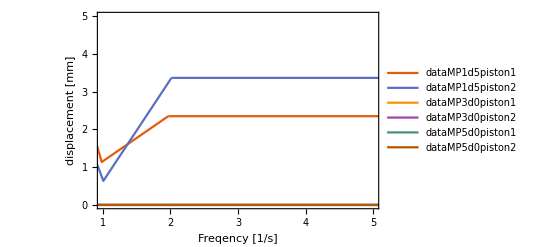

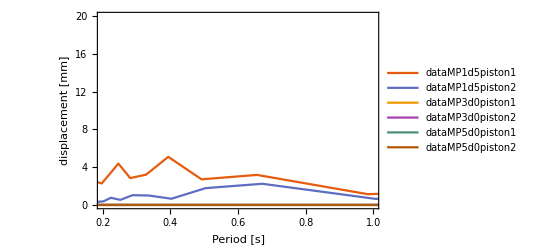

```mathematica
ListPlot[
Table[
Module[{},
{displacement,anlgetable,timetable,M,{xaxis,yaxis,zaxis},{min,max}}=calculate[DATA[[i]]];
Return[{inv[#1],#2}&@@@interpolateAndFourier[timetable,displacement[[;;,3]]]]]
,{i,1,Length@DATA,1}]
,PlotLegends->names
,PlotRange->{{1,5},{0,5}}
,Evaluate[plot2Doption]
,FrameLabel->{"Freqency [1/s]","displacement [mm]"}
]

(*フーリエ解析*)
ListPlot[
Table[
Module[{},
{displacement,anlgetable,timetable,M,{xaxis,yaxis,zaxis},{min,max}}=calculate[DATA[[i]]];
Return[{inv[#1],#2}&@@@interpolateAndFourier[timetable,displacement[[;;,3]]]]]
,{i,1,Length@DATA,1}]
,PlotLegends->names
,PlotRange->{{0.2,1},{0,20}}
,Evaluate[plot2Doption]
,FrameLabel->{"Period [s]","displacement [mm]"}
]
```